### Start choosing the example:

```mathematica
t=9;
beta = 1;
A=.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
g[m]
```

m

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{3,I2}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.010963 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
jt29==0&&u38==205&&u40==155
and the rules are:
<|j18→80,j19→30,u47→15,j14→80,j15→110,j16→30,j17→110,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→80,jt28→80-jt29,jt30→jt29,jt31→-jt29,jt32→-jt29,jt33→30+jt29,jt34→0,jt35→30,jt36→110,jt37→0,u41→15,u44→-80+u38,u45→-110+125,u46→-30+u40,u48→u38,u49→u40,u39→125,u42→u38,u43→u40|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j14-j20+IntM[j14-j20,1->2],j15-j21+IntM[j15-j21,2->4],j16-j22+IntM[j16-j22,3->2]}

DataToEquations: Done.

{0.046716,Null}

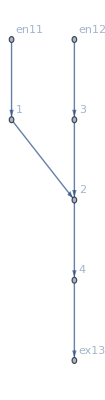

<|j14→80,j15→110,j16→30,j17→110,j18→80,j19→30,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→80,jt28→80,jt29→0,jt30→0,jt31→0,jt32→0,jt33→30,jt34→0,jt35→30,jt36→110,jt37→0,u38→205,u39→125,u40→155,u41→15,u42→205,u43→155,u44→125,u45→15,u46→125,u47→15,u48→205,u49→155|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,I2->30,U1->15}];//Timing
MFGEquations["FG"]
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==74.5834&&j15-j21-u39+u45==103.974&&j16-j22-u40+u46==26.1022

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.48322×10^-17

FRX1: nonlinear: 
j14-j20-u38+u44==74.5834&&j15-j21-u39+u45==103.974&&j16-j22-u40+u46==26.1022

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.48322×10^-17

<|j14→80,j15→110,j16→30,j17→110,j18→80,j19→30,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→80,jt28→80,jt29→0,jt30→0,jt31→0,jt32→0,jt33→30,jt34→0,jt35→30,jt36→110,jt37→0,u38→26.4423,u39→21.0258,u40→24.9236,u41→15,u42→26.4423,u43→24.9236,u44→21.0258,u45→15,u46→21.0258,u47→15,u48→26.4423,u49→24.9236|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0483×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0483×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→21.5012,u108→18.3398,u109→20.9562,u110→15,u111→21.5012,u112→20.9562,u113→18.3398,u114→15,u115→18.3398,u116→15,u117→21.5012,u118→20.9562|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.33236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.33236×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→25.5193,u108→20.4954,u109→24.2394,u110→15,u111→25.5193,u112→24.2394,u113→20.4954,u114→15,u115→20.4954,u116→15,u117→25.5193,u118→24.2394|>

```mathematica
alpha = 0.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

NIntegrate::inumr: The integrand M[80,MFGraphs`Private`x,1->2]^(-1+MFGraphs`Private`alpha) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand M[110,MFGraphs`Private`x,2->4]^(-1+MFGraphs`Private`alpha) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FRX1: nonlinear: 
j14-j20-u38+u44==80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j15-j21-u39+u45==110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j16-j22-u40+u46==30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u46]^2+Abs[80-u38+u46]^2+Abs[30-u40+u46]^2)),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-u38+u46&&j15-j21-u39+u45==125-u46&&j16-j22-u40+u46==30-u40+u46

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u39]^2+Abs[80-u38+u39]^2+Abs[30+u39-u40]^2)),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j15-j21-u39+u45==110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j16-j22-u40+u46==30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u46]^2+Abs[80-u38+u46]^2+Abs[30-u40+u46]^2)),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-u38+u46&&j15-j21-u39+u45==125-u46&&j16-j22-u40+u46==30-u40+u46

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u39]^2+Abs[80-u38+u39]^2+Abs[30+u39-u40]^2)),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j15-j21-u39+u45==110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j16-j22-u40+u46==30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u46]^2+Abs[80-u38+u46]^2+Abs[30-u40+u46]^2)),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-u38+u46&&j15-j21-u39+u45==125-u46&&j16-j22-u40+u46==30-u40+u46

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u39]^2+Abs[80-u38+u39]^2+Abs[30+u39-u40]^2)),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j15-j21-u39+u45==110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j16-j22-u40+u46==30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u46]^2+Abs[80-u38+u46]^2+Abs[30-u40+u46]^2)),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-u38+u46&&j15-j21-u39+u45==125-u46&&j16-j22-u40+u46==30-u40+u46

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u39]^2+Abs[80-u38+u39]^2+Abs[30+u39-u40]^2)),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j15-j21-u39+u45==110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]&&j16-j22-u40+u46==30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u46]^2+Abs[80-u38+u46]^2+Abs[30-u40+u46]^2)),(√(Abs[-u40+u46+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u46+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u46+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

FRX1: nonlinear: 
j14-j20-u38+u44==80-u38+u46&&j15-j21-u39+u45==125-u46&&j16-j22-u40+u46==30-u40+u46

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[125-u39]^2+Abs[80-u38+u39]^2+Abs[30+u39-u40]^2)),(√(Abs[u39-u40+30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[-u38+u39+80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[15-u39+110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))/(√(Abs[30-30 NIntegrate[1/M[30,MFGraphs`Private`x,3->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[80-80 NIntegrate[1/M[80,MFGraphs`Private`x,1->2]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2+Abs[110-110 NIntegrate[1/M[110,MFGraphs`Private`x,2->4]^(1-MFGraphs`Private`alpha),{MFGraphs`Private`x,0,1}]]^2))]

<|j14→80,j15→110,j16→30,j17→110,j18→80,j19→30,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→80,jt28→80,jt29→0,jt30→0,jt31→0,jt32→0,jt33→30,jt34→0,jt35→30,jt36→110,jt37→0,u41→15,u42→u38,u43→u40,u44→u39,u45→15,u46→u39,u47→15,u48→u38,u49→u40|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.6479×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.6479×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→118.768,u108→73.8023,u109→93.399,u110→15,u111→118.768,u112→93.399,u113→73.8023,u114→15,u115→73.8023,u116→15,u117→118.768,u118→93.399|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.57004×10^-13,ComplexInfinity]

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→205,u108→125,u109→155,u110→15,u111→205,u112→155,u113→125,u114→15,u115→125,u116→15,u117→205,u118→155|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.07055×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.07055×10^-16

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→952.896,u108→588.99,u109→679.535,u110→15,u111→952.896,u112→679.535,u113→588.99,u114→15,u115→588.99,u116→15,u117→952.896,u118→679.535|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.49007×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.49007×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→76975.9,u108→54135.4,u109→55829.9,u110→15,u111→76975.9,u112→55829.9,u113→54135.4,u114→15,u115→54135.4,u116→15,u117→76975.9,u118→55829.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54095×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54095×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→1.18884×10^6,u108→898799.,u109→908525.,u110→15,u111→1.18884×10^6,u112→908525.,u113→898799.,u114→15,u115→898799.,u116→15,u117→1.18884×10^6,u118→908525.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87912×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87912×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→3.02767×10^11,u108→2.78714×10^11,u109→2.78731×10^11,u110→15,u111→3.02767×10^11,u112→2.78731×10^11,u113→2.78714×10^11,u114→15,u115→2.78714×10^11,u116→15,u117→3.02767×10^11,u118→2.78731×10^11|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.48287×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.48287×10^-17

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→8.5312×10^20,u108→8.47516×10^20,u109→8.47516×10^20,u110→15,u111→8.5312×10^20,u112→8.47516×10^20,u113→8.47516×10^20,u114→15,u115→8.47516×10^20,u116→15,u117→8.5312×10^20,u118→8.47516×10^20|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.06128×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.06128×10^-16

<|j83→80,j84→110,j85→30,j86→110,j87→80,j88→30,j89→0,j90→0,j91→0,j92→0,j93→0,j94→0,jt100→0,jt101→0,jt102→30,jt103→0,jt104→30,jt105→110,jt106→0,jt95→0,jt96→80,jt97→80,jt98→0,jt99→0,u107→5.23663×10^106,u108→3.03173×10^106,u109→3.85857×10^106,u110→15,u111→5.23663×10^106,u112→3.85857×10^106,u113→3.03173×10^106,u114→15,u115→3.03173×10^106,u116→15,u117→5.23663×10^106,u118→3.85857×10^106|>

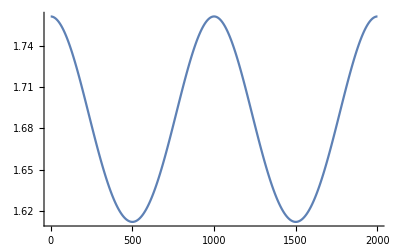
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]&/@MFGEquations["BEL"]
```

```mathematica
jv=Values[MFGEquations["jvars"]]/.FFR
```

{80,110,30,110,80,30,0,0,0,0,0,0}

```mathematica
a=1
```

1

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

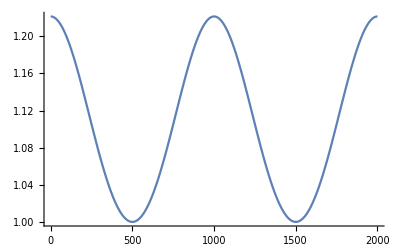
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

```mathematica
Plot[{0,Values[(mfunc[#])/.JTJNZ]},{x,0,1},PlotLabel->"m"#]&/@BEL
Plot[Join[Last/@Data["Exit Vertices and Terminal Costs"],Values[(ufunc[#])/.Join[JTJNZ,URNZ]]],{y,0,1},PlotLabel->"u"#]&/@BEL
```

### Ricardo’s input

the way we use some functions has changed, we need to provide the edge (or anything, for now)

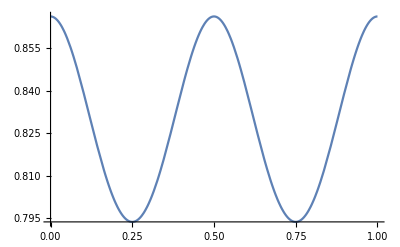

```mathematica
Plot[M[1,x,edge],{x,0,1}]
```

```mathematica
jv=Values[MFGEquations["jvars"]]/.FFR
```

{80,110,30,110,80,30,0,0,0,0,0,0}

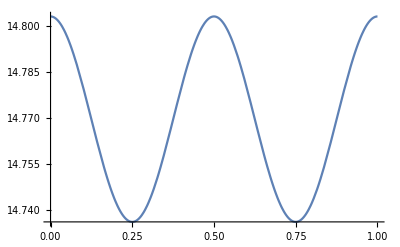
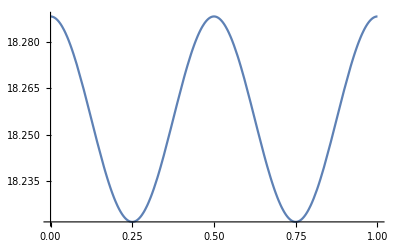
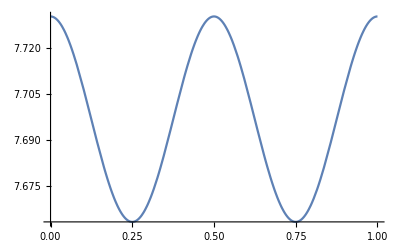
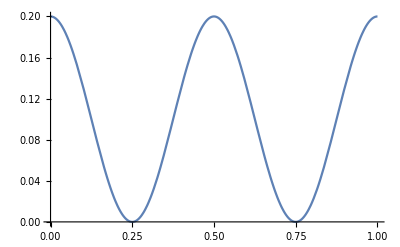
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[M[#,x,edge],{x,0,1}]&/@jv
```

```mathematica
jv=jv//DeleteDuplicates
```

{80,110,30,0}

```mathematica
Plot[M[#,x,edge],{x,0,1}]&/@jv
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}